## To Do & Notes

...

## Global Path Configure

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Network Project/compareFS_v0.1/NDN-EB-algo

```mathematica
fileName = "topo-geant.txt";
rawdata = Import[fileName];
data = StringSplit[rawdata,"\n"];
```

```mathematica
topoName = data⟦1⟧;
nodeName = Table[StringSplit[node,"\t"]⟦1⟧,{node,data⟦6;;27⟧}]
links =Table[
ele⟦1⟧<->ele⟦2⟧,
{ele,Table[StringSplit[link,"\t"],{link,data⟦32;;68⟧ }]}
]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V}

{A<->B,A<->C,B<->C,B<->Q,B<->D,B<->G,C<->U,D<->E,D<->F,D<->T,E<->G,F<->G,F<->H,F<->Q,F<->S,G<->I,G<->P,G<->U,H<->I,H<->L,H<->J,H<->R,J<->K,K<->L,L<->M,M<->N,N<->O,N<->Q,O<->P,P<->Q,Q<->R,Q<->U,R<->S,R<->T,S<->T,S<->V,U<->V}

## Visualization & Centrality Analysis

G | 0.0497003
H | 0.0488448
Q | 0.0480899
B | 0.047373
S | 0.0465996
D | 0.0463971
L | 0.0463184
U | 0.0462064
N | 0.0461069
F | 0.0458407
R | 0.0453314
C | 0.0451798
P | 0.0447358
K | 0.044659
T | 0.0443673
J | 0.0441189
M | 0.0439899
O | 0.0439372
A | 0.0433625
V | 0.0432292
E | 0.0428974
I | 0.0427143

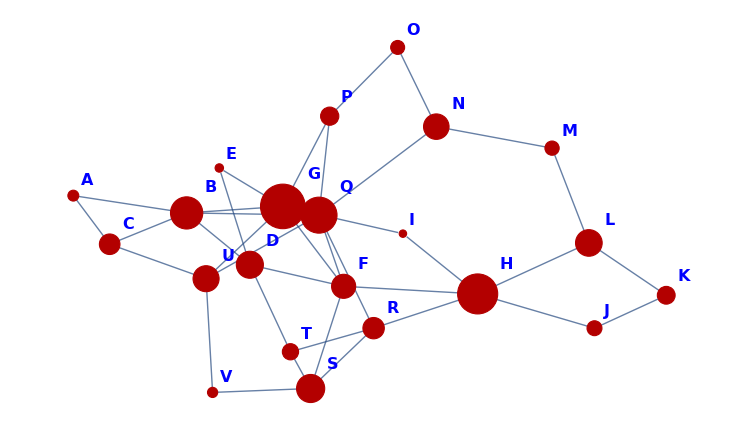

```mathematica
g = Graph[links,
VertexLabels-> "Name",
VertexLabelStyle->Directive[Blue,Bold,16]
];
prScroe = PageRankCentrality[g,0.1];
TableForm[Reverse[SortBy[{VertexList[g],prScroe}ᵀ,Last]]]
HighlightGraph[g,VertexList[g],VertexSize-> Thread[VertexList[g]-> Rescale[prScroe]+0.2]]
```

```mathematica
TableForm[Table[FindShortestPath[g,"G",node],{node,VertexList[g]}]]
```

G | B | A |  | 
G | B |  |  | 
G | B | C |  | 
G | B | Q |  | 
G | B | D |  | 
G |  |  |  | 
G | U |  |  | 
G | E |  |  | 
G | F |  |  | 
G | B | D | T | 
G | F | H |  | 
G | F | S |  | 
G | I |  |  | 
G | P |  |  | 
G | F | H | L | 
G | F | H | J | 
G | B | Q | R | 
G | F | H | L | K
G | B | Q | N | M
G | B | Q | N | 
G | P | O |  | 
G | U | V |  |

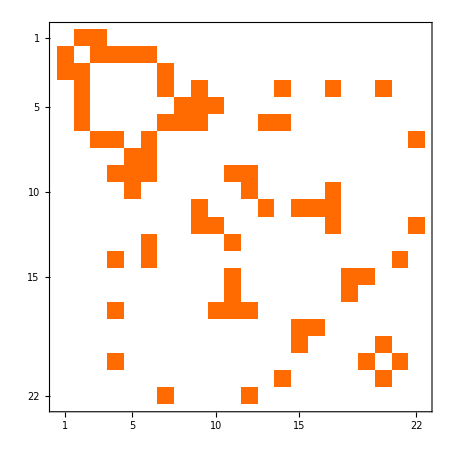

```mathematica
MatrixPlot[AdjacencyMatrix[%56]]
```

## Network Analysis

```mathematica
GraphCenter[%20]
```

{F,R}

```mathematica
GraphPeriphery[%20]
```

{A,C,K}

```mathematica
GraphRadius[%20]
```

3

```mathematica
GraphDiameter[%20]
```

6